capa con flow límite Potential

capa de la límite Tamaño

5333.33

0.00537864

0.0672329

del flujo potencial Solucion

2 D del Gráfica problema

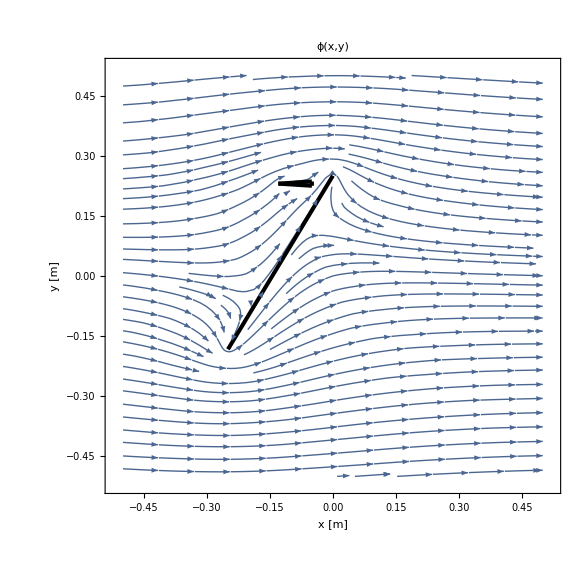

Cálculo del Lift

-10

1.31347

1.35193

0.407731

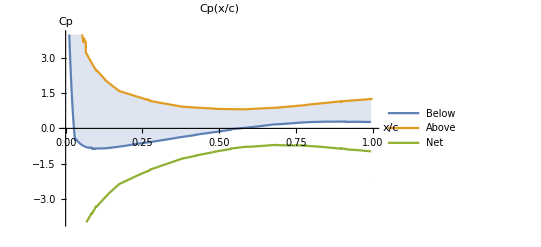

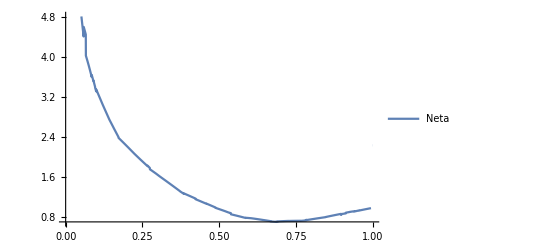

```mathematica
Potential flow (con capa límite)

ang=Pi/6;
s=0.05;d=-0.02;
Needs["NDSolve`FEM`"];
Vin=1.0;
a=1.5;b=1.5;L=0.25;t=0.00025;L2=0.08;
Tamaño de la capa límite
visco=1.5*10^(-5);
Rey=Vin*L2/visco
δ=4.91*L2/Sqrt[Rey]
m=δ/L2
Solucion del flujo potencial
bm=ToBoundaryMesh["Coordinates"->{{-a,-b},{a,-b},{a,b},{-a,b},{-t-2*L*Sin[ang],L-2*L*Cos[ang]},{-t-2*L*Sin[ang]+2*t*Cos[ang],L-2*L*Cos[ang]-2*t*Sin[ang]},{-t+2*t*Cos[ang],L-2*t*Sin[ang]},{-t,L},{-s-L2,L+d},{-s,L+d-δ},{-s,L+d+t*2+δ},{-s-L2,L+d+t*2}},"BoundaryElements"->{LineElement[{{1,2},{2,3},{3,4},{4,1}}],LineElement[{{5,6},{6,7},{7,8},{8,5}}],LineElement[{{9,10},{10,11},{11,12},{12,9}}]   }];
mesh=ToElementMesh[bm,"BoundaryMeshGenerator"->{"Continuation"},"RegionHoles"->{{-t-L*Sin[ang]+t*Cos[ang],L-L*Cos[ang]-t*Sin[ang]},{-s-L2/2,L+d+t}},MaxCellMeasure->0.0001,"MaxBoundaryCellMeasure"->0.001];
sol=NDSolveValue[{Laplacian[u[x,y],{x,y}]==NeumannValue[Vin,x==-a]+NeumannValue[-Vin,x==a],DirichletCondition[u[a,0]==0,x==a&&y==0]},u,Element[{x,y},mesh],"ExtrapolationHandler"->{(Indeterminate&),"WarningMessage"->True}];
ClearAll[v,p];

Gráfica del problema 2D
v[x_,y_]:=Evaluate[Grad[sol[x,y],{x,y},"Cartesian"]];
StreamPlot[v[x,y],{x,-0.5,0.5},{y,-0.5,0.5},AspectRatio->Automatic,Epilog->{Thickness[0.005],Line[  {{-2*L*Sin[ang],L-2*L*Cos[ang]},{0,L}}],Line[{{-s-L2,L+d+t},{-s,L+d+t+δ}}],Line[{{-s-L2,L+d+t},{-s,L+d+t-δ}}],Line[{{-s,L+d+t+δ},{-s,L+d+t-δ}}  ]} ,StreamPoints->Fine ,FrameLabel->{"x [m]","y [m]"},LabelStyle->FontSize->15 ,PlotLabel->Style["ϕ(x,y)",FontSize->20]]
Cálculo del Lift
pr=-10
rho=1.2;cte=0.5*rho*Vin^2 +101*10^3;
Cp[x0_,y0_]:=(
x1=-s-L2+x0*L2; y1=L+d+y0;
((cte-0.5*rho*((v[x1,y1][[1]])^2 +(v[x1,y1][[2]])^2 ))-101*10^3)/(0.5*rho*Vin^2)
)
CpDown[x0_]:=(
y0=-m*x0;
Cp[x0,y0]
)
CpUp[x0_]:=(
y0=t*2+m*x0;
Cp[x0,y0]
)
Lift=NIntegrate[CpDown[x]-CpUp[x] ,{x,0.05,1},AccuracyGoal->2]
Angulo=ArcTan[(v[-s-L2,L+d][[2]])/(-1*v[-s-L2,L+d][[1]])]
LiftFlat=2*Pi*Angulo*(0.5*rho*Vin^2*L2)

Plot[{CpDown[x],CpUp[x],(CpDown[x]-CpUp[x])},{x,0,1},Filling->{1->{2}},PlotLegends->{"Below","Above","Net"},ScalingFunctions->{Identity,"Reverse"},PlotRange->{{0,1},{-4,4}},AxesLabel->{"x/c","Cp"},LabelStyle->FontSize->15 ,PlotLabel->Style["Cp(x/c)",FontSize->20]]
Plot[CpDown[x]-CpUp[x] ,{x,0,1},PlotLegends->{"Neta"}]
```

```mathematica
Función para calcular Lift;
lift[s_,d_,ang_]:=({
Needs["NDSolve`FEM`"];
Vin=1.0;
a=1.5;b=1.5;L=0.25;t=0.00025;L2=0.08;
visco=1.5*10^(-5);
Rey=Vin*L2/visco;
δ=4.91*L2/Sqrt[Rey];
m=δ/L2;
bm=ToBoundaryMesh["Coordinates"->{{-a,-b},{a,-b},{a,b},{-a,b},{-t-2*L*Sin[ang],L-2*L*Cos[ang]},{-t-2*L*Sin[ang]+2*t*Cos[ang],L-2*L*Cos[ang]-2*t*Sin[ang]},{-t+2*t*Cos[ang],L-2*t*Sin[ang]},{-t,L},{-s-L2,L+d},{-s,L+d-δ},{-s,L+d+t*2+δ},{-s-L2,L+d+t*2}},"BoundaryElements"->{LineElement[{{1,2},{2,3},{3,4},{4,1}}],LineElement[{{5,6},{6,7},{7,8},{8,5}}],LineElement[{{9,10},{10,11},{11,12},{12,9}}]   }];
mesh=ToElementMesh[bm,"BoundaryMeshGenerator"->{"Continuation"},"RegionHoles"->{{-t-L*Sin[ang]+t*Cos[ang],L-L*Cos[ang]-t*Sin[ang]},{-s-L2/2,L+d+t}},MaxCellMeasure->0.001,"MaxBoundaryCellMeasure"->0.0001];
sol=NDSolveValue[{Laplacian[u[x,y],{x,y}]==NeumannValue[Vin,x==-a]+NeumannValue[-Vin,x==a],DirichletCondition[u[a,0]==0,x==a&&y==0]},u,Element[{x,y},mesh],"ExtrapolationHandler"->{(Indeterminate&),"WarningMessage"->True}];
ClearAll[v,p];
v[x_,y_]:=Evaluate[Grad[sol[x,y],{x,y},"Cartesian"]];

rho=1.2;cte=0.5*rho*Vin^2 +101*10^3;
Cp[x0_,y0_]:=(
x1=-s-L2+x0*L2; y1=L+d+y0;
((cte-0.5*rho*((v[x1,y1][[1]])^2 +(v[x1,y1][[2]])^2 ))-101*10^3)/(0.5*rho*Vin^2)
);
CpDown[x0_]:=(
y0=-t-m*x0;
Cp[x0,y0]
);
CpUp[x0_]:=(
y0=t+m*x0;
Cp[x0,y0]
);
Lift=NIntegrate[CpDown[x]-CpUp[x] ,{x,0.05,1},AccuracyGoal->2]
});

Quiet[   lift[0.05,-0.02,0][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/12][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/10][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/9][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/8][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/7][[1]]   ]
Quiet[   lift[0.05,-0.02,Pi/6][[1]]   ]
```

1.37149

1.39063

1.38203

1.33994

1.34204

1.33227

1.28937

```mathematica
l={};
For[i=1,i≤0.12*100,i++, (*variar s de 1 a 12 cm*)
For[j=-10,j≤0.1*100,j++, (*variar d de -10 a 10 cm*)
k={{i/100.0,j/100.0},0.33*(Pi/4)Quiet[lift[i/100.0,j/100.0,0][[1]] ]}; l=Insert[l,k,-1]
]]
cero=Interpolation[l]

clear[l];
l={};
For[i=1.5,i≤0.12*100,i++, (*variar s de 1.5 a 12 cm*)
For[j=-6.5,j≤0.1*100,j++, (*variar d de -6.5 a 10 cm*)
k={{i/100.0,j/100.0},0.33*(Pi/4)Quiet[lift[i/100.0,j/100.0,10*Pi/180][[1]] ]}; l=Insert[l,k,-1]
]]
diez=Interpolation[l]

clear[l];
l={};
For[i=2,i≤0.12*100,i++, (*variar s de 2 a 12 cm*)
For[j=-4.5,j≤0.1*100,j++, (*variar d de -4.5 a 10 cm*)
k={{i/100.0,j/100.0},0.33*(Pi/4)Quiet[lift[i/100.0,j/100.0,20*Pi/180][[1]] ]}; l=Insert[l,k,-1]
]]
veinte=Interpolation[l]

clear[l];
l={};
For[i=2.5,i≤0.12*100,i++, (*variar s de 2.5 a 12 cm*)
For[j=-3.5,j≤0.1*100,j++, (*variar d de -3.5 a 10 cm*)
k={{i/100.0,j/100.0},0.33*(Pi/4)Quiet[lift[i/100.0,j/100.0,30*Pi/180][[1]] ]}; l=Insert[l,k,-1]
]]
treinta=Interpolation[l]
```

InterpolatingFunction[{{0.01, 0.12}, {-0.1, 0.1}}, <>]

```mathematica
Plot3D[cero[x,y],{x,0.01,0.12},{y,-0.1,0.1}]
```

-Graphics3D-

```mathematica
Plot3D[diez[x,y],{x,0.015,0.115},{y,-0.065,0.095}]
```

-Graphics3D-

```mathematica
Plot3D[veinte[x,y],{x,0.02,0.12},{y,-0.045,0.095}]
```

-Graphics3D-

```mathematica
Plot3D[treinta[x,y],{x,0.025,0.115},{y,-0.035,0.095}]
```

-Graphics3D-

```mathematica
surface0=Plot3D[cero[x,y],{x,0.01,0.12},{y,-0.1,0.1},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotLegends->{"0°"}];
surface10=Plot3D[diez[x,y],{x,0.015,0.115},{y,-0.065,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Red],PlotLegends->{"10°"};
surface20=Plot3D[veinte[x,y],{x,0.02,0.12},{y,-0.045,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Blue,PlotLegends->{"20°"}];
surface30=Plot3D[treinta[x,y],{x,0.025,0.115},{y,-0.035,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Green,PlotLegends->{"30°"}];
ceroG=Show[surface0,surface10,surface20,surface30,PlotLabel->Style["Lift(s,d) [N]",FontSize->20]]
```

```mathematica
%176
```

-Graphics3D-

```mathematica
diez
```

InterpolatingFunction[{{0.015, 0.115}, {-0.065, 0.095}}, <>]

```mathematica
Information[cero]
Information[diez]
Information[veinte]
Information[treinta]
```

Global`cero

cero=InterpolatingFunction[{{0.01,0.12},{-0.1,0.1}},{5,7,0,{12,21},{4,4},0,0,0,0,Automatic,{},{},False},{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12},{-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252},{0.291194,0.366435,0.480609,0.632628,0.74181,0.764163,0.771812,0.770129,0.757421,0.727842,0.663909,0.486539,0.302629,0.128865,-0.0411688,-0.209626,-0.345233,-0.375894,-0.291939,-0.216881,-0.175375,0.272176,0.329514,0.403521,0.487889,0.548514,0.58868,0.602457,0.604592,0.6,0.569991,0.507688,0.407923,0.295659,0.163189,0.0318055,-0.0611911,-0.1462,-0.175648,-0.170915,-0.147813,-0.134029,0.248134,0.296778,0.346549,0.400682,0.439777,0.474466,0.493266,0.497651,0.496684,0.462409,0.417784,0.346666,0.279446,0.190431,0.104045,0.0164579,-0.0425162,-0.0722142,-0.0902216,-0.0951056,-0.0809077,0.230914,0.267172,0.305175,0.34176,0.375388,0.396603,0.416317,0.414929,0.414871,0.388645,0.355895,0.311335,0.261488,0.196928,0.139257,0.0641836,0.0167324,-0.0176536,-0.0398649,-0.0440445,-0.0480016,0.212711,0.240097,0.270467,0.300126,0.324687,0.342001,0.355589,0.361967,0.355464,0.340723,0.306847,0.279135,0.226659,0.183277,0.132538,0.0955649,0.0558698,0.0219342,-0.00240923,-0.0137141,-0.0195727,0.196908,0.220688,0.244121,0.263009,0.28509,0.29641,0.31109,0.310568,0.310249,0.296933,0.269797,0.237734,0.209868,0.182976,0.141344,0.111202,0.074237,0.0504731,0.0298295,0.0121257,0.00483203,0.181684,0.201968,0.221248,0.239222,0.255097,0.261305,0.268392,0.271886,0.271701,0.261809,0.249894,0.232432,0.20505,0.170205,0.144957,0.114542,0.0891259,0.0679815,0.0485758,0.0317213,0.0188893,0.168853,0.18475,0.201751,0.216861,0.229187,0.235149,0.240265,0.244397,0.243414,0.230791,0.223993,0.20675,0.188595,0.166487,0.139954,0.119769,0.0974258,0.0807115,0.061152,0.0437102,0.0333476,0.156861,0.171586,0.185076,0.197121,0.20344,0.210859,0.214551,0.219976,0.219705,0.210594,0.202335,0.192813,0.170186,0.155055,0.138244,0.115693,0.0998069,0.082806,0.0672203,0.0524534,0.0425324,0.144637,0.158655,0.169751,0.181414,0.185236,0.19166,0.196979,0.195108,0.20049,0.189884,0.183234,0.177484,0.162231,0.145618,0.131514,0.115339,0.100574,0.0836121,0.0706502,0.0589794,0.0493209,0.134096,0.147323,0.156789,0.162803,0.169855,0.17433,0.17967,0.178483,0.177886,0.174741,0.168022,0.159681,0.149909,0.138713,0.123329,0.112769,0.0994775,0.0867391,0.0747175,0.0629938,0.0535211,0.125707,0.134267,0.1448,0.151063,0.155525,0.160188,0.163246,0.164309,0.162198,0.160251,0.154584,0.145133,0.138894,0.129208,0.118611,0.108594,0.0973505,0.086025,0.0762263,0.0673244,0.057728}},{Automatic,Automatic}]

Global`diez

diez=InterpolatingFunction[{{0.015,0.115},{-0.065,0.095}},{5,7,0,{11,17},{4,4},0,0,0,0,Automatic,{},{},False},{{0.015,0.025,0.035,0.045,0.055,0.065,0.075,0.085,0.095,0.105,0.115},{-0.065,-0.055,-0.045,-0.035,-0.025,-0.015,-0.005,0.005,0.015,0.025,0.035,0.045,0.055,0.065,0.075,0.085,0.095}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187},{0.68242,0.740599,0.747777,0.744096,0.70855,0.676821,0.613687,0.498167,0.340518,0.186898,0.0181307,-0.107099,-0.211146,-0.28329,-0.264401,-0.217209,-0.172725,0.516756,0.555838,0.577521,0.578239,0.561609,0.537014,0.484061,0.40026,0.298396,0.192683,0.0648155,-0.0207878,-0.0890176,-0.12703,-0.142717,-0.135999,-0.116197,0.424752,0.455119,0.470756,0.47239,0.460681,0.441795,0.397166,0.33885,0.269604,0.21399,0.129116,0.0631482,-0.0130245,-0.046462,-0.0681317,-0.0815964,-0.0760983,0.361531,0.380404,0.394384,0.399146,0.39437,0.377726,0.345033,0.301503,0.256541,0.203641,0.152107,0.087881,0.0449875,0.0057503,-0.0190353,-0.0364493,-0.0398916,0.313037,0.334247,0.342437,0.343758,0.342138,0.31905,0.309191,0.270194,0.225393,0.183915,0.149818,0.102693,0.0734434,0.0379048,0.0161251,-0.0014816,-0.0104712,0.278609,0.291563,0.29658,0.299396,0.300376,0.282678,0.270515,0.242785,0.215724,0.185888,0.153147,0.118249,0.0876386,0.0613871,0.0405159,0.0252665,0.011815,0.249594,0.257744,0.26928,0.268857,0.265753,0.257785,0.244685,0.222633,0.203674,0.179029,0.151887,0.123545,0.0987672,0.0733836,0.0561091,0.0441963,0.0286647,0.227706,0.23273,0.234122,0.234923,0.233908,0.23264,0.221301,0.199936,0.1867,0.16834,0.14777,0.125577,0.103894,0.085341,0.0660955,0.0517345,0.0388384,0.203085,0.210196,0.21322,0.214739,0.213566,0.208067,0.197364,0.188725,0.175712,0.164704,0.136405,0.122507,0.104643,0.0861121,0.0737007,0.0611107,0.0527986,0.186008,0.190961,0.193968,0.19353,0.193544,0.189236,0.183681,0.177303,0.159685,0.148338,0.133842,0.119856,0.104557,0.0900685,0.0778092,0.0656513,0.0553552,0.172563,0.175543,0.177427,0.179694,0.175919,0.174813,0.168323,0.159926,0.151005,0.141053,0.130788,0.117543,0.102921,0.0923651,0.0800667,0.0697174,0.0595083}},{Automatic,Automatic}]

Global`veinte

veinte=InterpolatingFunction[{{0.02,0.12},{-0.045,0.095}},{5,7,0,{11,15},{4,4},0,0,0,0,Automatic,{},{},False},{{0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12},{-0.045,-0.035,-0.025,-0.015,-0.005,0.005,0.015,0.025,0.035,0.045,0.055,0.065,0.075,0.085,0.095}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165},{0.775353,0.732154,0.681105,0.621083,0.53363,0.419565,0.28352,0.149161,0.0296946,-0.0965877,-0.157156,-0.213672,-0.205772,-0.178785,-0.14989,0.564772,0.553545,0.518194,0.474116,0.423679,0.351991,0.255037,0.165851,0.0826842,-0.0176888,-0.0632552,-0.109437,-0.112465,-0.110194,-0.0967289,0.448192,0.439383,0.423948,0.406008,0.361682,0.294265,0.237569,0.171403,0.117951,0.0535319,0.0065734,-0.0360426,-0.0525184,-0.0610565,-0.061266,0.373125,0.370115,0.364826,0.339819,0.310641,0.266211,0.220608,0.174841,0.121357,0.0906139,0.0386661,0.00744534,-0.00980629,-0.0230868,-0.0296223,0.327547,0.323649,0.308718,0.298813,0.275757,0.249202,0.207019,0.170804,0.129855,0.0935717,0.0661404,0.0373528,0.0164979,0.00508987,-0.00473475,0.290031,0.286416,0.271635,0.264021,0.245394,0.219881,0.193743,0.164958,0.137033,0.107752,0.0896124,0.0567537,0.0378048,0.0242714,0.0178164,0.25836,0.2563,0.251178,0.238744,0.226831,0.207185,0.186451,0.157982,0.140313,0.110241,0.0918659,0.0707024,0.0552441,0.0378263,0.0285943,0.230706,0.229927,0.226623,0.21836,0.205886,0.190051,0.176524,0.155455,0.13566,0.117412,0.0964067,0.0796729,0.0650895,0.0506719,0.0414046,0.206898,0.211165,0.204106,0.198745,0.189156,0.177047,0.165725,0.146286,0.132224,0.112618,0.0998021,0.088543,0.0693798,0.0586065,0.0485301,0.189291,0.189669,0.187082,0.184289,0.171536,0.165039,0.153344,0.137746,0.130354,0.115222,0.10072,0.0862562,0.0742471,0.0641891,0.0548989,0.175363,0.174532,0.171043,0.167112,0.160897,0.154324,0.141737,0.133305,0.121448,0.110532,0.098906,0.0866949,0.0770032,0.0675912,0.0596073}},{Automatic,Automatic}]

Global`treinta

treinta=InterpolatingFunction[{{0.025,0.115},{-0.035,0.095}},{5,7,0,{10,14},{4,4},0,0,0,0,Automatic,{},{},False},{{0.025,0.035,0.045,0.055,0.065,0.075,0.085,0.095,0.105,0.115},{-0.035,-0.025,-0.015,-0.005,0.005,0.015,0.025,0.035,0.045,0.055,0.065,0.075,0.085,0.095}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140},{0.759781,0.668182,0.578679,0.495625,0.382476,0.247817,0.118756,0.0217391,-0.0605767,-0.115694,-0.156223,-0.157148,-0.140124,-0.125721,0.553512,0.501862,0.451588,0.380178,0.285984,0.211806,0.136743,0.0601755,0.00392928,-0.0461101,-0.0694548,-0.0964134,-0.0868378,-0.0815484,0.439038,0.401232,0.355657,0.307018,0.254907,0.208643,0.141824,0.0888412,0.0481699,0.00836436,-0.0207571,-0.0350932,-0.0470976,-0.0485167,0.349807,0.327781,0.296088,0.269005,0.225532,0.194595,0.144662,0.107588,0.0673774,0.0379371,0.0127486,-0.00632009,-0.0173672,-0.0213247,0.298391,0.285739,0.264401,0.240765,0.212903,0.182495,0.147347,0.114713,0.0819433,0.0600762,0.0421221,0.0170898,0.00541417,-0.00176108,0.26178,0.257875,0.237413,0.221167,0.197658,0.171949,0.146264,0.120219,0.0943996,0.073292,0.052915,0.037326,0.0247347,0.0147042,0.235429,0.22904,0.212516,0.202701,0.186324,0.163657,0.142382,0.12318,0.100252,0.0823641,0.0646789,0.0490933,0.0396961,0.0280934,0.215193,0.208109,0.199927,0.186142,0.174776,0.158705,0.137544,0.120981,0.104062,0.0872805,0.0716597,0.0589339,0.0471331,0.0385451,0.194737,0.193474,0.186036,0.175611,0.167787,0.147558,0.137303,0.119693,0.103967,0.0912364,0.0780936,0.0710279,0.0556809,0.0463872,0.185028,0.178127,0.167236,0.16336,0.151973,0.144238,0.131894,0.115291,0.104073,0.0929461,0.0811498,0.0704253,0.0613254,0.0521147}},{Automatic,Automatic}]

```mathematica
surface0=Plot3D[cero[x,y],{x,0.01,0.12},{y,-0.1,0.1},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15,PlotLegends->{"0°"} ]
surface10=Plot3D[diez[x,y],{x,0.015,0.115},{y,-0.065,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Red,PlotLegends->{"10°"}];
surface20=Plot3D[veinte[x,y],{x,0.02,0.12},{y,-0.045,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Blue,PlotLegends->{"20°"}];
surface30=Plot3D[treinta[x,y],{x,0.025,0.115},{y,-0.035,0.95},AxesLabel->{"s [m]","d [m]","L [N]"},LabelStyle->FontSize->15 ,PlotStyle->Green,PlotLegends->{"30°"}];
ceroG=Show[surface0,surface10,surface20,surface30,PlotLabel->Style["Lift(s,d) [N]",FontSize->20]]
```

-Graphics3D-

-Graphics3D-